```mathematica
$HistoryLength = 10;

findEvolutionOperator2D[Ham_]:=(
funcs=Array[ψ[#2 + 8*(#1- 1)][t]&,{8, 2}];
equations=Flatten@Join[Thread[Ham.funcs == ⅈ*D[funcs,t]],Thread[funcs==IdentityMatrix[8][[{1, 2, 3, 4, 5,6 , 7, 8}, {1, 2}]]/.t->0]];
NDSolveValue[equations,funcs,{t,0,Tmax}, AccuracyGoal->10, PrecisionGoal->10, EvaluationMonitor:>showStatus["t = "<>ToString[CForm[t]]]][[{1, 2}]]
)

fidelity2D[Mt_, Ma_] := (1/6)Sum[.25*Tr[Mt.(σI + σi).ConjugateTranspose[Mt].Ma.(σI + σi).ConjugateTranspose[Ma]], {σi, {σX, -σX, σY, -σY, σZ, -σZ}}];

Clear[fidelityToGate];
fidelityToGate[Ea_?NumericQ, Ba_?NumericQ, ωEin_?NumericQ, ωBin_?NumericQ, Tmaxin_?NumericQ, Ea2_?NumericQ,Ea3_?NumericQ,Ba2_?NumericQ,Ba3_?NumericQ, gate_] := (
HcorrectedAtStart = Hcorrected;

Clear[Eamp, Bamp, Eamp2, Bamp2, Eamp3, Bamp3];
Eamp[t_] := Ea*tanhWindow[t, Tmax/10, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax/10, Tmax]^2;
Eamp2[t_] := Ea2*tanhWindow[t, Tmax/10, Tmax]^2;
Bamp2[t_] := Ba2*tanhWindow[t, Tmax/10, Tmax]^2;
Eamp3[t_] := Ea3*tanhWindow[t, Tmax/10, Tmax]^2;
Bamp3[t_] := Ba3*tanhWindow[t, Tmax/10, Tmax]^2;
ωE = ωEin;
ωB = ωBin;
Tmax = Tmaxin;

(* simulate uncertainty in ΔE *)

ΔEold = ΔE;

ΔE = ΔEold - 100;
(*U = ConjugateTranspose[Urot[[{1, 2}, {1, 2}]]].findEvolutionOperator2D[Hcorrected];*)
U = findEvolutionOperator2D[HexactExtra];
F1 = fidelity2D[gate, U /. t->Tmax] // Chop;

ΔE = ΔEold;
(*U = ConjugateTranspose[Urot[[{1, 2}, {1, 2}]]].findEvolutionOperator2D[Hcorrected];*)
U = findEvolutionOperator2D[HexactExtra];
F2 = fidelity2D[gate, U /. t->Tmax] // Chop;

ΔE = ΔEold + 100;
(*U = ConjugateTranspose[Urot[[{1, 2}, {1, 2}]]].findEvolutionOperator2D[Hcorrected];*)
U = findEvolutionOperator2D[HexactExtra];
F3 = fidelity2D[gate, U /. t->Tmax] // Chop;

ΔE = ΔEold;

output = Mean[{F1, F2, F3}];

Print[{output, {F1, F2, F3}, {ΔE, B0, {Ea, Ea2, Ea3}, {Ba, Ba2, Ba3}, ωEin, ωBin, Tmax}}];

If[output > bestSoFar, (
bestSoFar = output;
bestParameters = {ΔE, B0, {Ea, Ea2, Ea3}, {Ba, Ba2, Ba3}, ωEin, ωBin, Tmax};
)];

Pause[2];

output
)

Clear[map]
map[x_, a_, b_] := a + (b - a)*x // Re

(* fidelityToY[EaD, BaD, ωED, ωBD] *)


setVariables[];
ΔE = 0;
(* DEFAULTS *)
B0D = B0;
EaD = 175.9346090620105;
BaD = 0.023107659216482147;
ωED =(* 2*π*ϵ0 - 3*10^9;*)3.461510856750805*^10;
ωBD = (*2*π*B0*γe - 3*10^9;*)3.446651302498991*^10;

Print["----------------------------------------" <> ToString[i] <> "----------------------------------------"];
TimeConstrained[(
bestSoFar = 0;
bestParameters = {};

NMaximize[
{
fidelityToGate[
map[x1, EaD*.5, EaD*1.5],
 map[x2, .95, 1.05]*map[x1, BaD*.5, BaD*1.5],
 map[x3, .9, 1.1]*ωED, 
map[x4, .9, 1.1]*ωBD,
5π/(map[x3, .9, 1.1]*ωED - map[x4, .9, 1.1]*ωBD) // Re ,
map[x5, -EaD/2, EaD/2],
map[x6, -EaD/2, EaD/2],
map[x7, -BaD/2, BaD/2],
map[x8, -BaD/2, BaD/2],
σY],
0 < x1 < 1,
0 < x2 < 1,
0 < x3 < 1,
0 < x4 < 1,
0 < x5 < 1,
0 < x6 < 1,
0 < x7 < 1,
0 < x8 < 1
},
{{x1,.3, .7}, {x2, .3, .7}, {x3, .3, .7}, {x4,.3, .7}, {x5,.3, .7},  {x6,.3, .7},  {x7,.3, .7},  {x8,.3, .7}},
Method->{"NelderMead", "RandomSeed"->RandomInteger[{0, 10000}]},
MaxIterations->10000
]

), 60*60*10
]

Do[(
Beep[];
Pause[.5];
), {i, 1, 10}]

clearVariables[]
```

----------------------------------------i----------------------------------------

{0.309046,{0.312585,0.302695,0.311858},{0,0.201123,{159.766,20.2435,-30.0064},{0.020835,-0.0039694,0.00237631},3.49607×10^10,3.45×10^10,3.40998×10^-8}}

{0.333307,{0.33331,0.333307,0.333304},{0,0.201123,{152.779,19.4474,-25.6153},{0.0203359,0.0015001,-0.00325708},3.36299×10^10,3.42853×10^10,-2.39662×10^-8}}

{0.328166,{0.328575,0.327218,0.328705},{0,0.201123,{179.64,-0.674706,-1.02863},{0.0238451,0.000899888,-0.000962696},3.44076×10^10,3.34×10^10,1.55901×10^-8}}

{0.335146,{0.334787,0.335226,0.335424},{0,0.201123,{145.258,13.851,28.8757},{0.0188194,-0.00239192,-0.000836655},3.36462×10^10,3.32436×10^10,3.90086×10^-8}}

{0.333322,{0.333322,0.333324,0.33332},{0,0.201123,{178.907,24.9831,-4.63409},{0.0235257,0.00386653,0.000645835},3.40243×10^10,3.51507×10^10,-1.39454×10^-8}}

{0.167468,{0.179114,0.146032,0.177258},{0,0.201123,{153.051,-15.0005,-30.4091},{0.0203742,0.0015037,0.00291494},3.50849×10^10,3.31684×10^10,8.19607×10^-9}}

{0.333313,{0.333312,0.333316,0.333309},{0,0.201123,{154.57,17.5298,21.7194},{0.0200883,-0.00141517,-0.00248183},3.39064×10^10,3.47508×10^10,-1.8604×10^-8}}

{0.333319,{0.333318,0.333322,0.333318},{0,0.201123,{195.301,-23.9741,15.0444},{0.026033,-0.00364973,0.00273212},3.33467×10^10,3.4323×10^10,-1.609×10^-8}}

{0.231087,{0.244351,0.2066,0.242309},{0,0.201123,{158.375,10.1073,31.0259},{0.0211625,-0.00125039,-0.00208299},3.50026×10^10,3.39796×10^10,1.53539×10^-8}}

{0.333323,{0.333323,0.333322,0.333323},{0,0.201123,{178.098,35.3788,39.2543},{0.0232289,-0.00310622,-0.00388168},3.31462×10^10,3.52399×10^10,-7.50271×10^-9}}

{0.333308,{0.33331,0.333307,0.333306},{0,0.201123,{177.705,16.5889,-20.1235},{0.0229464,-0.000816092,0.000666568},3.27644×10^10,3.47437×10^10,-7.93593×10^-9}}

{0.333308,{0.33331,0.333307,0.333305},{0,0.201123,{180.799,5.539,43.3795},{0.0238688,0.00269124,-0.00422017},3.22573×10^10,3.42842×10^10,-7.74962×10^-9}}

{0.333307,{0.33331,0.333307,0.333305},{0,0.201123,{161.214,28.0107,25.5037},{0.0208789,-0.0017302,-0.00169553},3.22728×10^10,3.56053×10^10,-4.71361×10^-9}}

{0.33332,{0.333321,0.333319,0.333319},{0,0.201123,{165.821,20.8393,18.8706},{0.0216093,-0.00107268,-0.00151232},3.28065×10^10,3.50539×10^10,-6.9892×10^-9}}

{0.333312,{0.333314,0.333311,0.333311},{0,0.201123,{191.336,8.23661,61.2119},{0.024576,-0.00297361,0.00103505},3.28446×10^10,3.49121×10^10,-7.59757×10^-9}}

{0.333321,{0.333324,0.333317,0.333322},{0,0.201123,{165.95,22.8194,-3.32476},{0.0213476,-0.00558097,0.00331194},3.43641×10^10,3.50702×10^10,-2.22452×10^-8}}

{0.333313,{0.333311,0.333323,0.333307},{0,0.201123,{166.105,13.3271,64.3779},{0.0218278,-0.00326485,-0.000913455},3.42569×10^10,3.46923×10^10,-3.60764×10^-8}}

{0.471069,{0.484754,0.4832,0.445251},{0,0.201123,{146.167,22.952,-16.166},{0.0194157,-0.00118014,-0.00176906},3.45297×10^10,3.4469×10^10,2.585×10^-7}}

{0.214776,{0.223806,0.196903,0.22362},{0,0.201123,{123.582,30.3097,-54.855},{0.0166869,-0.000283405,-0.00317111},3.53723×10^10,3.42474×10^10,1.39639×10^-8}}

{0.333327,{0.333326,0.333329,0.333326},{0,0.201123,{180.831,15.0143,13.8552},{0.0238755,-0.00267982,0.00192601},3.36237×10^10,3.45599×10^10,-1.67798×10^-8}}

{0.333322,{0.333322,0.33332,0.333322},{0,0.201123,{172.978,19.6389,-41.434},{0.0226153,-0.000683887,0.0010675},3.3115×10^10,3.45852×10^10,-1.0684×10^-8}}

{0.333308,{0.33331,0.333308,0.333306},{0,0.201123,{138.202,67.8432,-6.2202},{0.0177194,0.000442454,-0.00299423},3.39672×10^10,3.50201×10^10,-1.49192×10^-8}}

{0.333307,{0.333308,0.33331,0.333303},{0,0.201123,{181.026,-1.01973,9.72827},{0.0239002,-0.00262668,0.00130053},3.35018×10^10,3.44973×10^10,-1.57804×10^-8}}

{0.333328,{0.333329,0.333328,0.333327},{0,0.201123,{156.059,22.8857,-9.74539},{0.0204024,-0.00338055,0.00077144},3.44469×10^10,3.47696×10^10,-4.86795×10^-8}}

{0.471069,{0.484754,0.4832,0.445251},{0,0.201123,{146.167,22.952,-16.166},{0.0194157,-0.00118014,-0.00176906},3.45297×10^10,3.4469×10^10,2.585×10^-7}}

{0.333307,{0.333308,0.333309,0.333304},{0,0.201123,{155.994,21.8957,1.35231},{0.0205249,-0.00112641,-0.00164069},3.36681×10^10,3.47615×10^10,-1.43669×10^-8}}

{0.395161,{0.385855,0.398861,0.400768},{0,0.201123,{145.712,18.4015,6.35485},{0.0191168,-0.00178603,-0.00130286},3.4088×10^10,3.38563×10^10,6.77878×10^-8}}

{0.333314,{0.333316,0.333313,0.333314},{0,0.201123,{162.537,23.9675,-10.4001},{0.0214817,0.0013432,-0.000561611},3.4277×10^10,3.48098×10^10,-2.94813×10^-8}}

{0.333308,{0.33331,0.333307,0.333306},{0,0.201123,{162.132,29.1654,11.5441},{0.0213415,-0.00214318,-0.00282537},3.3838×10^10,3.48544×10^10,-1.5454×10^-8}}

{0.333317,{0.333315,0.333324,0.333312},{0,0.201123,{163.499,18.9832,-1.15543},{0.0216526,-0.00192998,0.000078477},3.40767×10^10,3.45144×10^10,-3.58892×10^-8}}

{0.333307,{0.333305,0.333315,0.333301},{0,0.201123,{170.734,-0.511037,-0.560794},{0.0227187,-0.00241493,0.000481532},3.39382×10^10,3.4396×10^10,-3.43159×10^-8}}

{0.333327,{0.333324,0.333329,0.333327},{0,0.201123,{159.572,21.2954,-28.8},{0.0210295,-0.000932014,-0.000350777},3.38224×10^10,3.45271×10^10,-2.22893×10^-8}}

{0.333307,{0.333306,0.333311,0.333303},{0,0.201123,{142.184,45.3976,-11.1931},{0.0185584,-0.000368843,-0.00238164},3.42485×10^10,3.47445×10^10,-3.16659×10^-8}}

{0.333306,{0.333304,0.333313,0.333301},{0,0.201123,{163.596,10.9661,-3.21887},{0.021665,-0.00190341,-0.000234262},3.40158×10^10,3.44831×10^10,-3.36126×10^-8}}

{0.333316,{0.333324,0.333309,0.333314},{0,0.201123,{151.113,22.9188,-12.9557},{0.0199142,-0.00228035,-0.000498809},3.44883×10^10,3.46193×10^10,-1.19947×10^-7}}

{0.471069,{0.484754,0.4832,0.445251},{0,0.201123,{146.167,22.952,-16.166},{0.0194157,-0.00118014,-0.00176906},3.45297×10^10,3.4469×10^10,2.585×10^-7}}

{0.333309,{0.333308,0.333312,0.333306},{0,0.201123,{151.08,22.4238,-7.40686},{0.0199734,-0.00115327,-0.00170487},3.40989×10^10,3.46152×10^10,-3.04246×10^-8}}

{0.572935,{0.610951,0.584676,0.523177},{0,0.201123,{145.94,20.6767,-4.90559},{0.0192661,-0.00148308,-0.00153596},3.43089×10^10,3.41626×10^10,1.07409×10^-7}}

{0.333318,{0.333317,0.333323,0.333315},{0,0.201123,{154.352,23.4598,-13.283},{0.0204514,0.000081528,-0.00116533},3.44034×10^10,3.46394×10^10,-6.65529×10^-8}}

{0.333313,{0.333312,0.333317,0.33331},{0,0.201123,{154.15,26.0587,-2.31094},{0.0203834,-0.00166166,-0.00229721},3.41839×10^10,3.46617×10^10,-3.28732×10^-8}}

{0.333311,{0.333308,0.333318,0.333308},{0,0.201123,{154.833,20.9676,-8.66073},{0.0205359,-0.00155506,-0.00084529},3.43032×10^10,3.44917×10^10,-8.33504×10^-8}}

{0.333317,{0.333322,0.333306,0.333323},{0,0.201123,{158.45,11.2205,-8.36341},{0.0210658,-0.00179754,-0.000643763},3.4234×10^10,3.44325×10^10,-7.91372×10^-8}}

{0.333309,{0.333308,0.33331,0.333309},{0,0.201123,{152.87,22.1237,-22.483},{0.0202261,-0.00105608,-0.00105992},3.41761×10^10,3.4498×10^10,-4.8785×10^-8}}

{0.74453,{0.708129,0.764925,0.760538},{0,0.201123,{153.388,20.1706,-14.8753},{0.0203407,-0.00157982,-0.000748963},3.45579×10^10,3.43783×10^10,8.74574×10^-8}}

{0.327912,{0.328665,0.326236,0.328834},{0,0.201123,{154.542,19.044,-18.6095},{0.020525,-0.00179309,-0.000271008},3.47874×10^10,3.42599×10^10,2.9775×10^-8}}

{0.450523,{0.519219,0.434088,0.398262},{0,0.201123,{151.728,19.9825,2.10286},{0.0201159,-0.00180795,-0.00131618},3.45763×10^10,3.44656×10^10,1.41901×10^-7}}

0.9983

{-600,0.415243}

{-580,0.426903}

{-560,0.440107}

{-540,0.455009}

{-520,0.471759}

{-500,0.490494}

{-480,0.511333}

{-460,0.53436}

{-440,0.55961}

{-420,0.587053}

{-400,0.616577}

{-380,0.64797}

{-360,0.680907}

{-340,0.714943}

{-320,0.749517}

{-300,0.783966}

{-280,0.817556}

{-260,0.849527}

{-240,0.879153}

{-220,0.905796}

{-200,0.928975}

{-180,0.948408}

{-160,0.964037}

{-140,0.976028}

{-120,0.984746}

{-100,0.990686}

{-80,0.994437}

{-60,0.996589}

{-40,0.997682}

{-20,0.998157}

{0,0.9983}

{20,0.998227}

{40,0.99787}

{60,0.996989}

{80,0.995194}

{100,0.991986}

{120,0.986814}

{140,0.979118}

{160,0.968411}

{180,0.95432}

{200,0.936645}

{220,0.915382}

{240,0.890734}

{260,0.863092}

{280,0.833001}

{300,0.801108}

{320,0.768107}

{340,0.73469}

{360,0.701495}

{380,0.669084}

{400,0.637915}

{420,0.60834}

{440,0.580607}

{460,0.554866}

{480,0.531189}

{500,0.509575}

{520,0.489978}

{540,0.472308}

{560,0.456453}

{580,0.442284}

{600,0.429664}

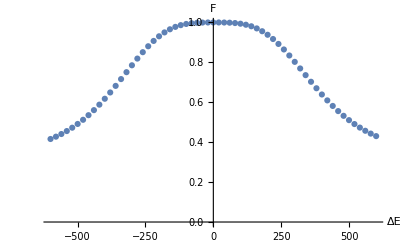

```mathematica
setVariables[]

(*{ΔE, B0, Ea, Ba, ωEin, ωBin, Tmaxin} = {-300, 0.20112299109490023, 222.4901014437078,0.014875274142248585,3.486194421243477*^10,3.472501636059094*^10,1.1474933117467306*^-7};
targetGate = σY;*)

(*{ΔE, B0, Ea, Ba, ωEin, ωBin, Tmaxin} = {0, 0.20112299109490023, 175.576,0.0230688,3.46162*10^10,3.44669*10^10,1.04864*10^-7};
targetGate = σY;*)

{ΔE, B0, Ea, Ba, ωEin, ωBin, Tmaxin} = {0,0.20112299109490023,175.89011507560335,0.023102752161808928,3.4624852817790726*^10,3.447574782262291*^10,1.0534833692372152*^-7};
targetGate = σY;

(*{ΔE, B0, Ea, Ba, ωEin, ωBin, Tmaxin} = {0,0.20112299109490023,220.15792727518044,0.02844144148279332,3.430428865007686*^10,3.414701350724212*^10,1.1985082691258685*^-7};
targetGate = σX;*)

(*{ΔE, B0, Ea, Ba, ωEin, ωBin, Tmaxin} = {0,0.20112299109490023,464.15147784830594,0.05966237754006056,3.308528133830387*^10,3.292892128373422*^10,1.205522470135874*^-7};
targetGate = σX;*)


Clear[Eamp, Bamp];
Eamp[t_] := Ea*tanhWindow[t, Tmax/10, Tmax]^2;
Bamp[t_] := Ba*tanhWindow[t, Tmax/10, Tmax]^2;
ωE = ωEin;
ωB = ωBin;
Tmax = Tmaxin;

Uax = ConjugateTranspose[Urot].findEvolutionOperator[Hcorrected];
U = Uax/. t->Tmax;
F = fidelity2D[targetGate, U[[{1, 2}, {1, 2}]]] // Chop;
Print[F]

Fs = {};
ΔEs = Table[e + ΔE, {e, -600, 600, 20}];

Do[
(
ΔE = deltaE;
Uax = ConjugateTranspose[Urot].findEvolutionOperator[Hcorrected];
(*Uex = findEvolutionOperator[Hexact];*)
(*M = ConjugateTranspose[Uex].Uax;*)

(*Plot[fidelity[M], {t, 0, Tmax}, PlotLabel->"Fidelity of Approximation to True Evolution"]*)

U = Uax/. t->Tmax;

F = fidelity2D[targetGate, U[[{1, 2}, {1, 2}]]] // Chop;

AppendTo[Fs, {ΔE, F}];

Pause[.5];

Print[{ΔE, F}];
),

{deltaE, ΔEs}
]

clearVariables[]

ListPlot[Fs, AxesLabel->{"ΔE", "F"}]
```

```mathematica
FsX2 = Fs;
```

```mathematica
FsY2 = Fs;
```

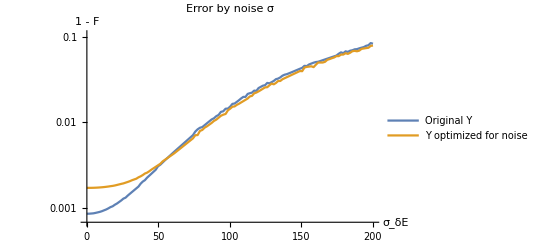

InterpolatingFunction::dmval: Input value {-999.959} lies outside the range of data in the interpolating function. Extrapolation will be used.

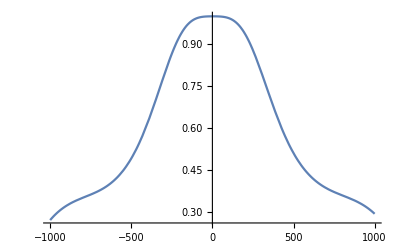

```mathematica
Finterpolated = Interpolation[FsY2];
Clear[FgivenSD]
FgivenSD[σ_, Fint_] := (
Mean[Fint[RandomVariate[NormalDistribution[0, σ], 10000]]]
)

Fints = {Interpolation[FsY], Interpolation[FsY2]};
(*1 - FgivenSD[0, Fints[[1]]]*)
LogPlot[{1 - FgivenSD[σ, Fints[[1]]], 1 - FgivenSD[σ, Fints[[2]]](*, 1 - FgivenSD[σ, Fints[[3]]]*)}, {σ, .0001, 200}, AxesLabel->{Subscript[σ, δE], "1 - F"}, PlotLegends->{"Original Y", "Y optimized for noise"}, PlotLabel->"Error by noise σ", PlotPoints->5, MaxRecursion->5]

Plot[Finterpolated[ΔE], {ΔE, -1000, 1000}]
```